## Getting Seperable Functions

```mathematica
Nasty[p_,q_]=1/2*Integrate[ⅇ^(ⅈ √(p^2+q^2-2 p q x)r μ)DiracDelta[r-a]2 π r^2,{r,0,∞},{μ,-1,1},{x,-1,1},Assumptions->{p∈Reals,q∈Reals,a∈Reals,p>0,q>0,a>0,p<1,q<1}]
```

(4 π Sin[a p] Sin[a q])/(p q)

## Functions

```mathematica
g[k_]:=Sin[a k]/(a k);
```

## Scattering Amplitude

```mathematica
G0[En_,H_]={{1/(En-H-ⅈ ϵ),0},{0,1/(En-H-β^2/m-ⅈ ϵ)}};
λ=4π a^2{{λo,λx},{λx,λc}};
```

```mathematica
Jmat[En_]=Limit[Integrate[G0[En,q^2/m]*g[q]g[q]*4π q^2/(2π)^3,{q,0,∞},Assumptions->{m>0,a≥0,β≥0,En∈Reals}],ϵ->0];
```

```mathematica
Δmat[En_]=IdentityMatrix[2]-λ.Jmat[En];

τ[En_]=Inverse[Δmat[En]].λ;
```

```mathematica
f[p_]=-m/(4π)Simplify[τ[p^2/m][[1,1]]g[p]g[p]]/. 1/(√(-p^2))->1/(-ⅈ p)/.√(-p^2)->-ⅈ p;
```

## Effective Range Expansion

```mathematica
ERE[p_,β_]=Series[1/f[p],{p,0,2}]+ⅈ p//Normal;
```

```mathematica
p0[β_]=Simplify[Coefficient[ERE[p,β],p,0]]/.√(β^2)->β/.√(1/β^2)->1/β
p1[β_]=Simplify[Coefficient[ERE[p,β],p,1]]/.√(β^2)->β/.√(1/β^2)->1/β
p2[β_]=Simplify[Coefficient[ERE[p,β],p,2]]/.√(β^2)->β/.√(1/β^2)->1/β
```

-(ⅇ^(a β) β^2 (1+a m λo)+m β (λc+a m λc λo-a m λx^2) Sinh[a β])/(a^2 m (ⅇ^(a β) β^2 λo+m β (λc λo-λx^2) Sinh[a β]))

0

(2 a^2 ⅇ^(2 a β) β^4 λo (-1+a m λo)+3 a ⅇ^(a β) m β^2 λx^2 Cosh[a β]+ⅇ^(a β) m β (-3 λx^2-3 a β λx^2+4 a^3 m β^2 λo (λc λo-λx^2)+2 a^2 β^2 (-2 λc λo+λx^2)) Sinh[a β]+2 a^2 m^2 β^2 (λc λo-λx^2) (λc (-1+a m λo)-a m λx^2) Sinh[a β]^2)/(6 a^2 m (ⅇ^(a β) β^2 λo+m β (λc λo-λx^2) Sinh[a β])^2)

```mathematica
T1[β_]=-1/p0[β]
```

(a^2 m (ⅇ^(a β) β^2 λo+m β (λc λo-λx^2) Sinh[a β]))/(ⅇ^(a β) β^2 (1+a m λo)+m β (λc+a m λc λo-a m λx^2) Sinh[a β])

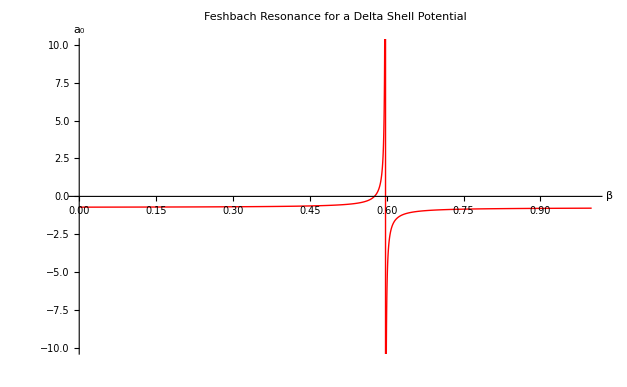

```mathematica
Params={λo->-.5,λc->-2,λx->-.1,m->.850645,a->1};

Bb=Plot[T1[β]/.Params,{β,0,1},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red];

Graph=Show[Bb,PlotRange->{-10,10},AxesLabel->{"β","a_0"},PlotLabel->"Feshbach Resonance for a Delta Shell Potential"]
```

```mathematica
Export["/home/cnewby/SeniorDesign/Final/DeltaGraph.eps",Graph]
```

/home/cnewby/SeniorDesign/Final/DeltaGraph.eps